## DelaunayEdges-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 18:55:10
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Generate a square tissue object with randomized centers

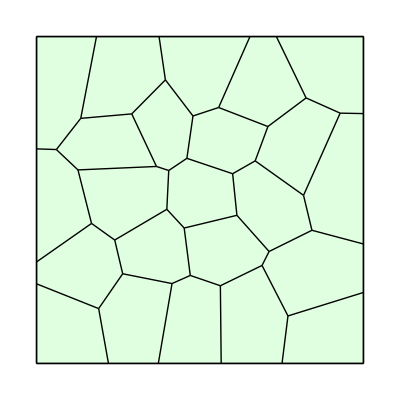

```mathematica
q=TemplateRandomSquareGrid[25, {0,0}, {10, 10}];
ShowTissue[q]
```

Find the centroids of the cells

```mathematica
v=Centroid[q]
```

{{0.95892,1.01117},{1.40267,2.94284},{0.6592,4.94024},{2.13807,6.70562},{0.748363,8.48549},{3.01338,1.33095},{3.63625,3.46339},{2.68445,5.08913},{3.93048,7.24114},{2.6334,8.81924},{4.77871,1.217},{5.70723,3.45731},{5.00227,5.18985},{5.76312,6.82988},{5.03188,9.03065},{6.59173,1.30837},{8.52779,2.82661},{7.1322,4.79983},{7.98171,6.73967},{6.92045,8.56906},{8.88213,0.904971},{9.27139,5.53014},{8.9372,8.97788}}

Find the Delaunay Triangulation of the centroids

```mathematica
de=DelaunayEdges[v]
```

{{{0.95892,1.01117},{1.40267,2.94284}},{{0.95892,1.01117},{0.6592,4.94024}},{{0.95892,1.01117},{3.01338,1.33095}},{{0.95892,1.01117},{4.77871,1.217}},{{0.95892,1.01117},{8.88213,0.904971}},{{1.40267,2.94284},{0.6592,4.94024}},{{1.40267,2.94284},{3.01338,1.33095}},{{1.40267,2.94284},{3.63625,3.46339}},{{1.40267,2.94284},{2.68445,5.08913}},{{0.6592,4.94024},{2.13807,6.70562}},{{0.6592,4.94024},{0.748363,8.48549}},{{0.6592,4.94024},{2.68445,5.08913}},{{2.13807,6.70562},{0.748363,8.48549}},{{2.13807,6.70562},{2.68445,5.08913}},{{2.13807,6.70562},{3.93048,7.24114}},{{2.13807,6.70562},{2.6334,8.81924}},{{0.748363,8.48549},{2.6334,8.81924}},{{3.01338,1.33095},{3.63625,3.46339}},{{3.01338,1.33095},{4.77871,1.217}},{{3.63625,3.46339},{2.68445,5.08913}},{{3.63625,3.46339},{4.77871,1.217}},{{3.63625,3.46339},{5.70723,3.45731}},{{3.63625,3.46339},{5.00227,5.18985}},{{2.68445,5.08913},{3.93048,7.24114}},{{2.68445,5.08913},{5.00227,5.18985}},{{3.93048,7.24114},{2.6334,8.81924}},{{3.93048,7.24114},{5.00227,5.18985}},{{3.93048,7.24114},{5.76312,6.82988}},{{3.93048,7.24114},{5.03188,9.03065}},{{2.6334,8.81924},{5.03188,9.03065}},{{4.77871,1.217},{5.70723,3.45731}},{{4.77871,1.217},{6.59173,1.30837}},{{4.77871,1.217},{8.88213,0.904971}},{{5.70723,3.45731},{5.00227,5.18985}},{{5.70723,3.45731},{6.59173,1.30837}},{{5.70723,3.45731},{8.52779,2.82661}},{{5.70723,3.45731},{7.1322,4.79983}},{{5.00227,5.18985},{5.76312,6.82988}},{{5.00227,5.18985},{7.1322,4.79983}},{{5.76312,6.82988},{5.03188,9.03065}},{{5.76312,6.82988},{7.1322,4.79983}},{{5.76312,6.82988},{7.98171,6.73967}},{{5.76312,6.82988},{6.92045,8.56906}},{{5.03188,9.03065},{6.92045,8.56906}},{{5.03188,9.03065},{8.9372,8.97788}},{{6.59173,1.30837},{8.52779,2.82661}},{{6.59173,1.30837},{8.88213,0.904971}},{{8.52779,2.82661},{7.1322,4.79983}},{{8.52779,2.82661},{8.88213,0.904971}},{{8.52779,2.82661},{9.27139,5.53014}},{{7.1322,4.79983},{7.98171,6.73967}},{{7.1322,4.79983},{9.27139,5.53014}},{{7.98171,6.73967},{6.92045,8.56906}},{{7.98171,6.73967},{9.27139,5.53014}},{{7.98171,6.73967},{8.9372,8.97788}},{{6.92045,8.56906},{8.9372,8.97788}},{{8.88213,0.904971},{9.27139,5.53014}},{{9.27139,5.53014},{8.9372,8.97788}}}

Plot the Delaunay Triangulation of the Centroids, and observe that the Delaunay of the centroids is not the same as the connectivity - there may be a missing or extra connection.

```mathematica
deCentroids=Graphics[Join[Point/@v, Line/@de]];
```

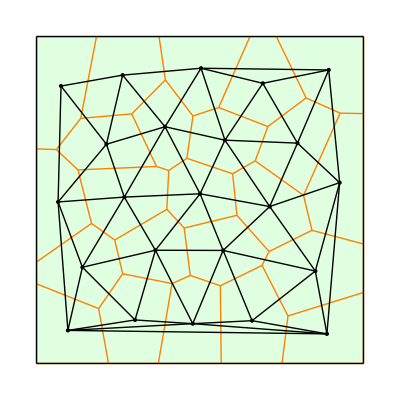

```mathematica
Show[ShowTissue[q, "EdgeStyles"-> Orange], deCentroids]
```

Observe that the Voronoi of the centroids is not the same as the original tissue.

```mathematica
bcv=BoundedCellVoronoi[v];
```

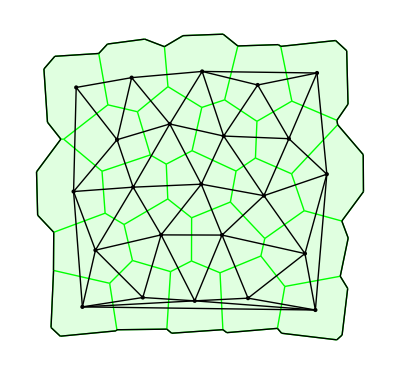

```mathematica
Show[ShowTissue[bcv, "EdgeStyles"-> Green], deCentroids]
```

#### Overlay the Voronoi Boundaries (purple, dotted) on the actual tissue

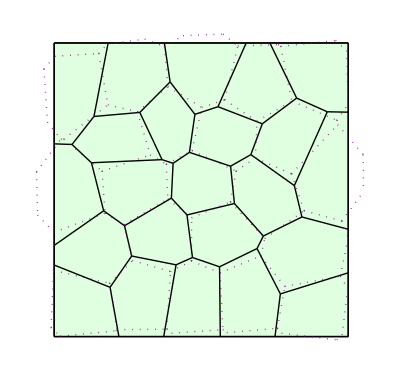

```mathematica
Show[ShowTissue[q], Graphics[{Purple, Dotted, Line/@EdgeVertices[bcv]}]]
```